```mathematica
v1 = {{0,0},{1,0},{2,0},{3,0},{4,0},{5,0.60},{6,2.67},{7,21.18},{8,198}};
v2 = {{0,0},{1,0},{2,0},{3,0},{4,0},{5,0.47},{6,.76},{7,1.29},{8,2.58},{9,4.29},{10,9.25},{11,27},{12,139.52},{13,1324}};
```

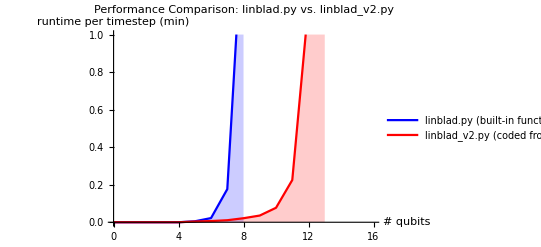

```mathematica
ListPlot[{{#[[1]],#[[2]]/120}&/@v1,{#[[1]],#[[2]]/120}&/@v2},PlotRange->{{0,16},{0,1}},Filling->Axis,Joined->True,PlotLabel->"Performance Comparison: linblad.py vs. linblad_v2.py",AxesLabel->{"# qubits","runtime per timestep (min)"},PlotLegends->{"linblad.py (built-in function)","linblad_v2.py (coded from scratch)"},PlotStyle->{Blue, Red}]
```